```mathematica
Quit[];
```

```mathematica
mmu=MaxMemoryUsed[]
SetDirectory[NotebookDirectory[]];
(* Global Properties *)
eV=27.211;
h=4.135667516×10^-15;
c=3×10^8;
shell={"s","p","p+","d","d+","f","f+","g","g+"};
RelOrbitals={"4s","5s","4p","4p+","5p","5p+","4d","4d+","5d","5d+","4f","4f+","5f","5f+","5g","5g+"};
jOrbitals={0.5,0.5,0.5,1.5,0.5,1.5,1.5,2.5,1.5,2.5,2.5,3.5,2.5,3.5,3.5,4.5};
(* s must ne first; nj, nj+ must be consecutive *) 
NonRelOrbitals={"4s","5s","4p","5p","4d","5d","4f","5f","5g"};
l={0,0,1,1,2,2,3,3,4};
MaxElectrons=2(2l+1);
spin={0.5,-0.5};

<<ReadAMBiTOutput`;
<<MBQCSpectra`;

FS=14; FF="Helvetica"; (* Plotting Font Size and Font*)
ImRes=600; (* Export Image Resolution dpi *)
```

1107273744

```mathematica
ION="12";
configs="df-df-df-0"; (* Which variation of configurations calculated to include *)
filenameMBQC="E1_Transitions3/Sn"<>ION<>"_0/"<>configs<>"/Sn"<>ION<>"+_E1.txt";
fileMBQC=Import[filenameMBQC,"CSV"];
filenameCI="E1_Transitions3/Sn"<>ION<>"/"<>configs<>"/Sn"<>ION<>"+_E1.txt";
fileCI=Import[filenameCI,"CSV"];
filename0diag="E1_Transitions3/Sn"<>ION<>"_0/"<>configs<>"/Sn"<>ION<>"+_E1.txt";
file0diag=Import[filename0diag,"CSV"];
```

```mathematica
{Shells,EnergyCSF,Num}=ReadLevels[fileMBQC];
L=Length[Shells];
TotalLines=L*(L-1)/2;
EnergyCSF=EnergyCSF eV;

Print["# of CI averaged states: ",L]
NumTotal=Total[Num];
T=SingleTransitionData[fileMBQC];
Ltran=Length[T];

(* Sn08 -> 15, Sn09 -> 16, Sn10 -> 17, Sn11 -> 20, Sn12 -> 22, Sn13 -> 23, Sn14 -> 24*)
G=22;
Cutoff=G; (*Lorenzian has range 2*Cutoff *)
Temp=26;
increment=0.005;
max=Max[EnergyCSF]+Cutoff+10;
min=Floor[Min[EnergyCSF]-Cutoff-10];
{z,Density}=LevelDensity[EnergyCSF,Num,G,increment,max,min,Cutoff];


{Emin,PsiE}=ComplexWaveEnergies[G,z,Density,increment,EnergyCSF,Num];
PsiE=PsiE-Emin;
z=z-Emin;
EnergyCSF=EnergyCSF-Emin;

Components=ComplexCoefficients2[G,EnergyCSF,Num,2*Cutoff];
Components2=Components^2;
Dspacing=Table[LevelSpacing3[PsiE,EnergyCSF[[i]],G],{i,1,L}];

{CONFIGS,NumPROJECT,NonRelConfigs,NumCONFIGS,RelConfigs}=NonRelativisticConfiguration[Shells,Num];

AverageJ=ConigurationAverageJ[CONFIGS];
AverageJall=ConstantArray[0,Length[NonRelConfigs]];
For[i=1,i≤Length[CONFIGS],i=i+1,
{
pos=Position[NonRelConfigs,CONFIGS[[i]]];
AverageJall[[posᵀ[[1]]]]=AverageJ[[i]];
}];
Jinitial=Table[Total[AverageJall*Components[[i]]]/Total[Components[[i]]],{i,1,L}];

nAverage=(RelConfigsᵀ/(2*jOrbitals+1))ᵀ;
Z=Total[Table[Num[[i]]*Exp[-EnergyCSF[[i]]/Temp],{i,1,L}]];
```

```mathematica
E1=Table[E1Transitions[i,j,Shells,T,nAverage],{i,1,L},{j,1,L}];
indicies=ListIndicies[L];

(* iPsi lower energy then jPsi *)
(* jPsi -> iPsi *)
Tic=AbsoluteTime[];
Efinal=EnergyCSF[[indicies[[1]]]];
Dspacing2=Dspacing[[indicies[[1]]]];
Einitial=EnergyCSF[[indicies[[2]]]];
Light=Einitial-Efinal+Shift;
Jin=Jinitial[[indicies[[2]]]];
NumLines=Num[[indicies[[1]]]]*Num[[indicies[[2]]]];

Cutoff=40;
Renorm=2/π*ArcTan[Cutoff/G];
StrengthNorm=Table[Main[i,Cutoff,Renorm,G,T,Light,indicies,Dspacing2,Jin,NumLines,E1,Ltran,Components2],
{i,1,TotalLines}];

Einstein=(2.0261*10^18)*(Light)^3/(4.1357*10^-15*3*10^8*10^10)^3 *StrengthNorm;
Intensity=Exp[-Einitial/Temp]*Einstein*Light/(4π Z);


Toc=AbsoluteTime[];
Print["Done MBQC, Time Taken: ",Toc-Tic];

{ECI,SCI,EINITIAL,EFINAL,IntensityCI,EinsteinCI}=DiscreteLevels[fileCI,Temp,Emin];
{Ediag,Sdiag,EINITIALdiag,EFINALdiag,Intensitydiag,Einsteindiag}=DiscreteLevels[file0diag,Temp,Emin];

Print[" "];
Print["Total States:          ",NumTotal];
Print["# CI Transitions:      ",Length[SCI]]; 
Print["# MBQC Transitions:    ",TotalLines]; 
Print["S CI:                  ",Total[SCI]];
Print["S MBQC Norm:           ",Total[StrengthNorm]];
Print["% diff Norm:           ",(Total[StrengthNorm]-Total[SCI])/Total[SCI]*100]
```

Done MBQC, Time Taken: 249.016386 ÷2

Total States:          38075

# CI Transitions:      1381863

# MBQC Transitions:    3240

S CI:                  19312.7

S MBQC Norm:           20500.1

% diff Norm:           6.14802

```mathematica
ClearAll[MBQCSpectrum,CISpectrum];
G=1;
EnergyRange=Range[0,300,0.1];

MBQCSpectrum=DiscreteSpectrum[Light,StrengthNorm,EnergyRange,G];
CISpectrum=DiscreteSpectrum[ECI,SCI,EnergyRange,G];
Diag0Spectrum=DiscreteSpectrum[Ediag,Sdiag,EnergyRange,G];
MBQCEinstein=DiscreteSpectrum[Light,Einstein,EnergyRange,G];
CIEinstein=DiscreteSpectrum[ECI,EinsteinCI,EnergyRange,G];
Diag0Einstein=DiscreteSpectrum[Ediag,Einsteindiag,EnergyRange,G];
MBQCIntensity=DiscreteSpectrum[Light,Intensity,EnergyRange,G];
CIIntensity=DiscreteSpectrum[ECI,IntensityCI,EnergyRange,G];
Diag0Intensity=DiscreteSpectrum[Ediag,Intensitydiag,EnergyRange,G];
```

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

Convolution Started

Convolution Finished

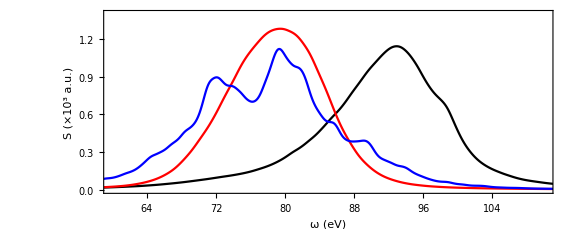

```mathematica
AR=1/2.5;

axis={{60,110},{0,1.4}};
discrete=False;

If[discrete==True,
{
im1=ListPlot[{Light,StrengthNorm}ᵀ,PlotRange->axis,Filling->Axis,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR,PlotMarkers->Automatic];
imA=ListPlot[{ECI,SCI}ᵀ,Filling->Axis,PlotRange->axis,PlotStyle->Black,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR,PlotMarkers->Automatic,PlotMarkers->Automatic];
imX=ListPlot[{Ediag,Sdiag}ᵀ,Filling->Axis,PlotRange->axis,PlotStyle->Red,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR,PlotMarkers->Automatic,PlotMarkers->Automatic];
im2=ListLinePlot[{EnergyRange,MBQCSpectrum}ᵀ,PlotRange->axis,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imB=ListLinePlot[{EnergyRange,CISpectrum}ᵀ,PlotRange->axis,PlotStyle->Black,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imY=ListLinePlot[{EnergyRange,Diag0Spectrum}ᵀ,PlotRange->axis,PlotStyle->Red,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
s1=Show[{imA,imB,imX,imY,im1,im2},Frame->{True,True,False,False},PlotRangePadding->0,FrameLabel->{"ω (eV)","S (a.u.)"},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],ImageSize->Large]
},{
im2=ListLinePlot[{EnergyRange,MBQCSpectrum/1000}ᵀ,PlotRange->axis,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imB=ListLinePlot[{EnergyRange,CISpectrum/1000}ᵀ,PlotRange->axis,PlotStyle->Black,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imY=ListLinePlot[{EnergyRange,Diag0Spectrum/1000}ᵀ,PlotRange->axis,PlotStyle->Red,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
s1=Show[{imB,imY,im2},Frame->{True,True,False,False},PlotRangePadding->0,FrameLabel->{"ω (eV)","S (×10^3 a.u.)"},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],ImageSize->Large]
}];
s1
```

```mathematica
Moment[WeightedData[Light,StrengthNorm],1]
2.355Sqrt[CentralMoment[WeightedData[Light,StrengthNorm],2]]
POS=Position[Light,_?(50<#<125&)];
Light2=Light[[POSᵀ[[1]]]];
S2=StrengthNorm[[POSᵀ[[1]]]];
Moment[WeightedData[Light2,S2],1]
2.355Sqrt[CentralMoment[WeightedData[Light2,S2],2]]
```

78.3058

20.4051

77.904

16.5603

```mathematica
Max[Light]
```

253.117

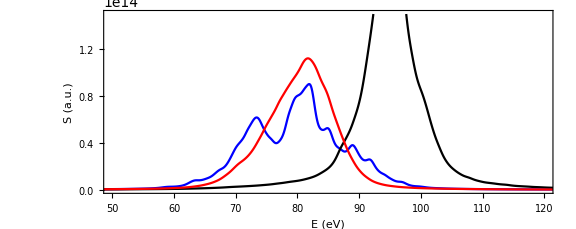

```mathematica
axis={{50,120},{0,150*10^12}};
discrete=False;

If[discrete==True,
{
im1=ListPlot[{Light,Einstein}ᵀ,PlotRange->axis,Filling->Axis,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR,PlotMarkers->Automatic];
imA=ListPlot[{ECI,EinsteinCI}ᵀ,Filling->Axis,PlotRange->axis,PlotStyle->Black,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR,PlotMarkers->Automatic,PlotMarkers->Automatic];
imX=ListPlot[{Ediag,Einsteindiag}ᵀ,Filling->Axis,PlotRange->axis,PlotStyle->Red,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR,PlotMarkers->Automatic,PlotMarkers->Automatic];
im2=ListLinePlot[{EnergyRange,MBQCEinstein}ᵀ,PlotRange->axis,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imB=ListLinePlot[{EnergyRange,CIEinstein}ᵀ,PlotRange->axis,PlotStyle->Black,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imY=ListLinePlot[{EnergyRange,Diag0Einstein}ᵀ,PlotRange->axis,PlotStyle->Red,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
s2=Show[{im1,im2,imA,imB,imX,imY},Frame->{True,True,False,False},PlotRangePadding->0,FrameLabel->{"E (eV)","S (a.u.)"},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF]]
},{
im2=ListLinePlot[{EnergyRange,MBQCEinstein}ᵀ,PlotRange->axis,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imB=ListLinePlot[{EnergyRange,CIEinstein}ᵀ,PlotRange->axis,PlotStyle->Black,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imY=ListLinePlot[{EnergyRange,Diag0Einstein}ᵀ,PlotRange->axis,PlotStyle->Red,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
s2=Show[{im2,imB,imY},Frame->{True,True,False,False},PlotRangePadding->0,FrameLabel->{"ΔE (eV)","a.u.)"},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF]]
}];
s2
```

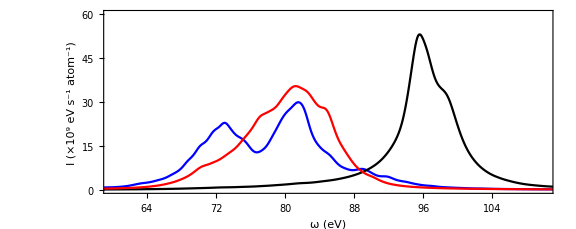

```mathematica
axis={{60,110},{0,60*10^0}};
discrete=False;

If[discrete==True,
{
im1=ListPlot[{Light,Intensity}ᵀ,PlotRange->axis,Filling->Axis,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR,PlotMarkers->Automatic];
imA=ListPlot[{ECI,IntensityCI}ᵀ,Filling->Axis,PlotRange->axis,PlotStyle->Black,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR,PlotMarkers->Automatic,PlotMarkers->Automatic];
imX=ListPlot[{Ediag,Intensitydiag}ᵀ,Filling->Axis,PlotRange->axis,PlotStyle->Red,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR,PlotMarkers->Automatic,PlotMarkers->Automatic];
im2=ListLinePlot[{EnergyRange,MBQCIntensity}ᵀ,PlotRange->axis,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imB=ListLinePlot[{EnergyRange,CIIntensity}ᵀ,PlotRange->axis,PlotStyle->Black,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imY=ListLinePlot[{EnergyRange,Diag0Intensity}ᵀ,PlotRange->axis,PlotStyle->Red,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
s3=Show[{im1,im2,imA,imB,imX,imY},Frame->{True,True,False,False},PlotRangePadding->0,FrameLabel->{"E (eV)","S (a.u.)"},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF]]
},{
im2=ListLinePlot[{EnergyRange,MBQCIntensity/10^9}ᵀ,PlotRange->axis,PlotStyle->Blue,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imB=ListLinePlot[{EnergyRange,CIIntensity/10^9}ᵀ,PlotRange->axis,PlotStyle->Black,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
imY=ListLinePlot[{EnergyRange,Diag0Intensity/10^9}ᵀ,PlotRange->axis,PlotStyle->Red,ImageSize->Large,LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],AspectRatio->AR];
s3=Show[{im2,imB,imY},Frame->{True,True,False,False},PlotRangePadding->0,FrameLabel->{"ω (eV)","I (×10^9 eV s^-1 atom^-1)"},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF]]
}];
s3
```